This is for x*sin(2*x)*exp(-10 * x**2)

```mathematica
x ={-1.2,-1.19519038,-1.19038076,-1.18557114,-1.18076152,-1.1759519,-1.17114228,-1.16633267,-1.16152305,-1.15671343,-1.15190381,-1.14709419,-1.14228457,-1.13747495,-1.13266533,-1.12785571,-1.12304609,-1.11823647,-1.11342685,-1.10861723,-1.10380762,-1.098998,-1.09418838,-1.08937876,-1.08456914,-1.07975952,-1.0749499,-1.07014028,-1.06533066,-1.06052104,-1.05571142,-1.0509018,-1.04609218,-1.04128257,-1.03647295,-1.03166333,-1.02685371,-1.02204409,-1.01723447,-1.01242485,-1.00761523,-1.00280561,-0.99799599,-0.99318637,-0.98837675,-0.98356713,-0.97875752,-0.9739479,-0.96913828,-0.96432866,-0.95951904,-0.95470942,-0.9498998,-0.94509018,-0.94028056,-0.93547094,-0.93066132,-0.9258517,-0.92104208,-0.91623246,-0.91142285,-0.90661323,-0.90180361,-0.89699399,-0.89218437,-0.88737475,-0.88256513,-0.87775551,-0.87294589,-0.86813627,-0.86332665,-0.85851703,-0.85370741,-0.8488978,-0.84408818,-0.83927856,-0.83446894,-0.82965932,-0.8248497,-0.82004008,-0.81523046,-0.81042084,-0.80561122,-0.8008016,-0.79599198,-0.79118236,-0.78637275,-0.78156313,-0.77675351,-0.77194389,-0.76713427,-0.76232465,-0.75751503,-0.75270541,-0.74789579,-0.74308617,-0.73827655,-0.73346693,-0.72865731,-0.7238477,-0.71903808,-0.71422846,-0.70941884,-0.70460922,-0.6997996,-0.69498998,-0.69018036,-0.68537074,-0.68056112,-0.6757515,-0.67094188,-0.66613226,-0.66132265,-0.65651303,-0.65170341,-0.64689379,-0.64208417,-0.63727455,-0.63246493,-0.62765531,-0.62284569,-0.61803607,-0.61322645,-0.60841683,-0.60360721,-0.5987976,-0.59398798,-0.58917836,-0.58436874,-0.57955912,-0.5747495,-0.56993988,-0.56513026,-0.56032064,-0.55551102,-0.5507014,-0.54589178,-0.54108216,-0.53627255,-0.53146293,-0.52665331,-0.52184369,-0.51703407,-0.51222445,-0.50741483,-0.50260521,-0.49779559,-0.49298597,-0.48817635,-0.48336673,-0.47855711,-0.47374749,-0.46893788,-0.46412826,-0.45931864,-0.45450902,-0.4496994,-0.44488978,-0.44008016,-0.43527054,-0.43046092,-0.4256513,-0.42084168,-0.41603206,-0.41122244,-0.40641283,-0.40160321,-0.39679359,-0.39198397,-0.38717435,-0.38236473,-0.37755511,-0.37274549,-0.36793587,-0.36312625,-0.35831663,-0.35350701,-0.34869739,-0.34388778,-0.33907816,-0.33426854,-0.32945892,-0.3246493,-0.31983968,-0.31503006,-0.31022044,-0.30541082,-0.3006012,-0.29579158,-0.29098196,-0.28617234,-0.28136273,-0.27655311,-0.27174349,-0.26693387,-0.26212425,-0.25731463,-0.25250501,-0.24769539,-0.24288577,-0.23807615,-0.23326653,-0.22845691,-0.22364729,-0.21883768,-0.21402806,-0.20921844,-0.20440882,-0.1995992,-0.19478958,-0.18997996,-0.18517034,-0.18036072,-0.1755511,-0.17074148,-0.16593186,-0.16112224,-0.15631263,-0.15150301,-0.14669339,-0.14188377,-0.13707415,-0.13226453,-0.12745491,-0.12264529,-0.11783567,-0.11302605,-0.10821643,-0.10340681,-0.09859719,-0.09378758,-0.08897796,-0.08416834,-0.07935872,-0.0745491,-0.06973948,-0.06492986,-0.06012024,-0.05531062,-0.050501,-0.04569138,-0.04088176,-0.03607214,-0.03126253,-0.02645291,-0.02164329,-0.01683367,-0.01202405,-0.00721443,-0.00240481,0.00240481,0.00721443,0.01202405,0.01683367,0.02164329,0.02645291,0.03126253,0.03607214,0.04088176,0.04569138,0.050501,0.05531062,0.06012024,0.06492986,0.06973948,0.0745491,0.07935872,0.08416834,0.08897796,0.09378758,0.09859719,0.10340681,0.10821643,0.11302605,0.11783567,0.12264529,0.12745491,0.13226453,0.13707415,0.14188377,0.14669339,0.15150301,0.15631263,0.16112224,0.16593186,0.17074148,0.1755511,0.18036072,0.18517034,0.18997996,0.19478958,0.1995992,0.20440882,0.20921844,0.21402806,0.21883768,0.22364729,0.22845691,0.23326653,0.23807615,0.24288577,0.24769539,0.25250501,0.25731463,0.26212425,0.26693387,0.27174349,0.27655311,0.28136273,0.28617234,0.29098196,0.29579158,0.3006012,0.30541082,0.31022044,0.31503006,0.31983968,0.3246493,0.32945892,0.33426854,0.33907816,0.34388778,0.34869739,0.35350701,0.35831663,0.36312625,0.36793587,0.37274549,0.37755511,0.38236473,0.38717435,0.39198397,0.39679359,0.40160321,0.40641283,0.41122244,0.41603206,0.42084168,0.4256513,0.43046092,0.43527054,0.44008016,0.44488978,0.4496994,0.45450902,0.45931864,0.46412826,0.46893788,0.47374749,0.47855711,0.48336673,0.48817635,0.49298597,0.49779559,0.50260521,0.50741483,0.51222445,0.51703407,0.52184369,0.52665331,0.53146293,0.53627255,0.54108216,0.54589178,0.5507014,0.55551102,0.56032064,0.56513026,0.56993988,0.5747495,0.57955912,0.58436874,0.58917836,0.59398798,0.5987976,0.60360721,0.60841683,0.61322645,0.61803607,0.62284569,0.62765531,0.63246493,0.63727455,0.64208417,0.64689379,0.65170341,0.65651303,0.66132265,0.66613226,0.67094188,0.6757515,0.68056112,0.68537074,0.69018036,0.69498998,0.6997996,0.70460922,0.70941884,0.71422846,0.71903808,0.7238477,0.72865731,0.73346693,0.73827655,0.74308617,0.74789579,0.75270541,0.75751503,0.76232465,0.76713427,0.77194389,0.77675351,0.78156313,0.78637275,0.79118236,0.79599198,0.8008016,0.80561122,0.81042084,0.81523046,0.82004008,0.8248497,0.82965932,0.83446894,0.83927856,0.84408818,0.8488978,0.85370741,0.85851703,0.86332665,0.86813627,0.87294589,0.87775551,0.88256513,0.88737475,0.89218437,0.89699399,0.90180361,0.90661323,0.91142285,0.91623246,0.92104208,0.9258517,0.93066132,0.93547094,0.94028056,0.94509018,0.9498998,0.95470942,0.95951904,0.96432866,0.96913828,0.9739479,0.97875752,0.98356713,0.98837675,0.99318637,0.99799599,1.00280561,1.00761523,1.01242485,1.01723447,1.02204409,1.02685371,1.03166333,1.03647295,1.04128257,1.04609218,1.0509018,1.05571142,1.06052104,1.06533066,1.07014028,1.0749499,1.07975952,1.08456914,1.08937876,1.09418838,1.098998,1.10380762,1.10861723,1.11342685,1.11823647,1.12304609,1.12785571,1.13266533,1.13747495,1.14228457,1.14709419,1.15190381,1.15671343,1.16152305,1.16633267,1.17114228,1.1759519,1.18076152,1.18557114,1.19038076,1.19519038,1.2};
y= {-3.76496672*10^-07,-4.26882685*10^-07,-4.83691819*10^-07,-5.47700947*10^-07,-6.19775585*10^-07,-7.00879357*10^-07,-7.92084394*10^-07,-8.94582749*10^-07,-1.00969892*10^-06,-1.13890358*10^-06,-1.28382861*10^-06,-1.44628356*10^-06,-1.62827366*10^-06,-1.83201948*10^-06,-2.05997840*10^-06,-2.31486810*10^-06,-2.59969206*10^-06,-2.91776745*10^-06,-3.27275541*10^-06,-3.66869406*10^-06,-4.11003432*10^-06,-4.60167882*10^-06,-5.14902420*10^-06,-5.75800684*10^-06,-6.43515256*10^-06,-7.18763028*10^-06,-8.02331020*10^-06,-8.95082656*10^-06,-9.97964552*10^-06,-1.11201383*10^-05,-1.23836603*10^-05,-1.37826357*10^-05,-1.53306494*10^-05,-1.70425452*10^-05,-1.89345317*10^-05,-2.10242955*10^-05,-2.33311234*10^-05,-2.58760326*10^-05,-2.86819106*10^-05,-3.17736646*10^-05,-3.51783812*10^-05,-3.89254972*10^-05,-4.30469817*10^-05,-4.75775300*10^-05,-5.25547700*10^-05,-5.80194826*10^-05,-6.40158348*10^-05,-7.05916282*10^-05,-7.77985620*10^-05,-8.56925118*10^-05,-9.43338250*10^-05,-1.03787633*10^-04,-1.14124181*10^-04,-1.25419177*10^-04,-1.37754156*10^-04,-1.51216870*10^-04,-1.65901694*10^-04,-1.81910049*10^-04,-1.99350855*10^-04,-2.18341000*10^-04,-2.39005830*10^-04,-2.61479663*10^-04,-2.85906328*10^-04,-3.12439727*10^-04,-3.41244413*10^-04,-3.72496200*10^-04,-4.06382796*10^-04,-4.43104451*10^-04,-4.82874639*10^-04,-5.25920757*10^-04,-5.72484844*10^-04,-6.22824334*10^-04,-6.77212815*10^-04,-7.35940819*10^-04,-7.99316630*10^-04,-8.67667110*10^-04,-9.41338541*10^-04,-1.02069748*10^-03,-1.10613165*10^-03,-1.19805080*10^-03,-1.29688761*10^-03,-1.40309861*10^-03,-1.51716506*10^-03,-1.63959391*10^-03,-1.77091864*10^-03,-1.91170023*10^-03,-2.06252803*10^-03,-2.22402065*10^-03,-2.39682682*10^-03,-2.58162628*10^-03,-2.77913056*10^-03,-2.99008381*10^-03,-3.21526354*10^-03,-3.45548135*10^-03,-3.71158360*10^-03,-3.98445202*10^-03,-4.27500430*10^-03,-4.58419454*10^-03,-4.91301370*10^-03,-5.26248992*10^-03,-5.63368878*10^-03,-6.02771346*10^-03,-6.44570476*10^-03,-6.88884107*10^-03,-7.35833816*10^-03,-7.85544887*10^-03,-8.38146268*10^-03,-8.93770508*10^-03,-9.52553683*10^-03,-1.01463530*10^-02,-1.08015821*10^-02,-1.14926844*10^-02,-1.22211507*10^-02,-1.29885009*10^-02,-1.37962816*10^-02,-1.46460647*10^-02,-1.55394443*10^-02,-1.64780348*10^-02,-1.74634681*10^-02,-1.84973900*10^-02,-1.95814577*10^-02,-2.07173359*10^-02,-2.19066930*10^-02,-2.31511974*10^-02,-2.44525127*10^-02,-2.58122937*10^-02,-2.72321814*10^-02,-2.87137977*10^-02,-3.02587403*10^-02,-3.18685771*10^-02,-3.35448404*10^-02,-3.52890206*10^-02,-3.71025598*10^-02,-3.89868457*10^-02,-4.09432043*10^-02,-4.29728930*10^-02,-4.50770935*10^-02,-4.72569042*10^-02,-4.95133328*10^-02,-5.18472881*10^-02,-5.42595729*10^-02,-5.67508750*10^-02,-5.93217600*10^-02,-6.19726624*10^-02,-6.47038777*10^-02,-6.75155541*10^-02,-7.04076841*10^-02,-7.33800964*10^-02,-7.64324477*10^-02,-7.95642148*10^-02,-8.27746860*10^-02,-8.60629543*10^-02,-8.94279089*10^-02,-9.28682287*10^-02,-9.63823744*10^-02,-9.99685824*10^-02,-1.03624858*10^-01,-1.07348970*10^-01,-1.11138445*10^-01,-1.14990560*10^-01,-1.18902342*10^-01,-1.22870561*10^-01,-1.26891727*10^-01,-1.30962089*10^-01,-1.35077630*10^-01,-1.39234067*10^-01,-1.43426850*10^-01,-1.47651164*10^-01,-1.51901928*10^-01,-1.56173795*10^-01,-1.60461159*10^-01,-1.64758155*10^-01,-1.69058665*10^-01,-1.73356321*10^-01,-1.77644517*10^-01,-1.81916410*10^-01,-1.86164931*10^-01,-1.90382794*10^-01,-1.94562508*10^-01,-1.98696385*10^-01,-2.02776554*10^-01,-2.06794975*10^-01,-2.10743452*10^-01,-2.14613649*10^-01,-2.18397104*10^-01,-2.22085252*10^-01,-2.25669434*10^-01,-2.29140923*10^-01,-2.32490941*10^-01,-2.35710679*10^-01,-2.38791320*10^-01,-2.41724058*10^-01,-2.44500122*10^-01,-2.47110801*10^-01,-2.49547461*10^-01,-2.51801578*10^-01,-2.53864754*10^-01,-2.55728747*10^-01,-2.57385493*10^-01,-2.58827130*10^-01,-2.60046027*10^-01,-2.61034804*10^-01,-2.61786361*10^-01,-2.62293900*10^-01,-2.62550948*10^-01,-2.62551383*10^-01,-2.62289458*10^-01,-2.61759821*10^-01,-2.60957538*10^-01,-2.59878116*10^-01,-2.58517520*10^-01,-2.56872195*10^-01,-2.54939084*10^-01,-2.52715643*10^-01,-2.50199862*10^-01,-2.47390273*10^-01,-2.44285968*10^-01,-2.40886612*10^-01,-2.37192447*10^-01,-2.33204309*10^-01,-2.28923630*10^-01,-2.24352443*10^-01,-2.19493391*10^-01,-2.14349724*10^-01,-2.08925302*10^-01,-2.03224593*10^-01,-1.97252669*10^-01,-1.91015203*10^-01,-1.84518459*10^-01,-1.77769286*10^-01,-1.70775104*10^-01,-1.63543896*10^-01,-1.56084192*10^-01,-1.48405049*10^-01,-1.40516041*10^-01,-1.32427232*10^-01,-1.24149160*10^-01,-1.15692814*10^-01,-1.07069606*10^-01,-9.82913506*10^-02,-8.93702351*10^-02,-8.03187922*10^-02,-7.11498708*10^-02,-6.18766059*10^-02,-5.25123869*10^-02,-4.30708258*10^-02,-3.35657239*10^-02,-2.40110387*10^-02,-1.44208493*10^-02,-4.80932256*10^-03,4.80932256*10^-03,1.44208493*10^-02,2.40110387*10^-02,3.35657239*10^-02,4.30708258*10^-02,5.25123869*10^-02,6.18766059*10^-02,7.11498708*10^-02,8.03187922*10^-02,8.93702351*10^-02,9.82913506*10^-02,1.07069606*10^-01,1.15692814*10^-01,1.24149160*10^-01,1.32427232*10^-01,1.40516041*10^-01,1.48405049*10^-01,1.56084192*10^-01,1.63543896*10^-01,1.70775104*10^-01,1.77769286*10^-01,1.84518459*10^-01,1.91015203*10^-01,1.97252669*10^-01,2.03224593*10^-01,2.08925302*10^-01,2.14349724*10^-01,2.19493391*10^-01,2.24352443*10^-01,2.28923630*10^-01,2.33204309*10^-01,2.37192447*10^-01,2.40886612*10^-01,2.44285968*10^-01,2.47390273*10^-01,2.50199862*10^-01,2.52715643*10^-01,2.54939084*10^-01,2.56872195*10^-01,2.58517520*10^-01,2.59878116*10^-01,2.60957538*10^-01,2.61759821*10^-01,2.62289458*10^-01,2.62551383*10^-01,2.62550948*10^-01,2.62293900*10^-01,2.61786361*10^-01,2.61034804*10^-01,2.60046027*10^-01,2.58827130*10^-01,2.57385493*10^-01,2.55728747*10^-01,2.53864754*10^-01,2.51801578*10^-01,2.49547461*10^-01,2.47110801*10^-01,2.44500122*10^-01,2.41724058*10^-01,2.38791320*10^-01,2.35710679*10^-01,2.32490941*10^-01,2.29140923*10^-01,2.25669434*10^-01,2.22085252*10^-01,2.18397104*10^-01,2.14613649*10^-01,2.10743452*10^-01,2.06794975*10^-01,2.02776554*10^-01,1.98696385*10^-01,1.94562508*10^-01,1.90382794*10^-01,1.86164931*10^-01,1.81916410*10^-01,1.77644517*10^-01,1.73356321*10^-01,1.69058665*10^-01,1.64758155*10^-01,1.60461159*10^-01,1.56173795*10^-01,1.51901928*10^-01,1.47651164*10^-01,1.43426850*10^-01,1.39234067*10^-01,1.35077630*10^-01,1.30962089*10^-01,1.26891727*10^-01,1.22870561*10^-01,1.18902342*10^-01,1.14990560*10^-01,1.11138445*10^-01,1.07348970*10^-01,1.03624858*10^-01,9.99685824*10^-02,9.63823744*10^-02,9.28682287*10^-02,8.94279089*10^-02,8.60629543*10^-02,8.27746860*10^-02,7.95642148*10^-02,7.64324477*10^-02,7.33800964*10^-02,7.04076841*10^-02,6.75155541*10^-02,6.47038777*10^-02,6.19726624*10^-02,5.93217600*10^-02,5.67508750*10^-02,5.42595729*10^-02,5.18472881*10^-02,4.95133328*10^-02,4.72569042*10^-02,4.50770935*10^-02,4.29728930*10^-02,4.09432043*10^-02,3.89868457*10^-02,3.71025598*10^-02,3.52890206*10^-02,3.35448404*10^-02,3.18685771*10^-02,3.02587403*10^-02,2.87137977*10^-02,2.72321814*10^-02,2.58122937*10^-02,2.44525127*10^-02,2.31511974*10^-02,2.19066930*10^-02,2.07173359*10^-02,1.95814577*10^-02,1.84973900*10^-02,1.74634681*10^-02,1.64780348*10^-02,1.55394443*10^-02,1.46460647*10^-02,1.37962816*10^-02,1.29885009*10^-02,1.22211507*10^-02,1.14926844*10^-02,1.08015821*10^-02,1.01463530*10^-02,9.52553683*10^-03,8.93770508*10^-03,8.38146268*10^-03,7.85544887*10^-03,7.35833816*10^-03,6.88884107*10^-03,6.44570476*10^-03,6.02771346*10^-03,5.63368878*10^-03,5.26248992*10^-03,4.91301370*10^-03,4.58419454*10^-03,4.27500430*10^-03,3.98445202*10^-03,3.71158360*10^-03,3.45548135*10^-03,3.21526354*10^-03,2.99008381*10^-03,2.77913056*10^-03,2.58162628*10^-03,2.39682682*10^-03,2.22402065*10^-03,2.06252803*10^-03,1.91170023*10^-03,1.77091864*10^-03,1.63959391*10^-03,1.51716506*10^-03,1.40309861*10^-03,1.29688761*10^-03,1.19805080*10^-03,1.10613165*10^-03,1.02069748*10^-03,9.41338541*10^-04,8.67667110*10^-04,7.99316630*10^-04,7.35940819*10^-04,6.77212815*10^-04,6.22824334*10^-04,5.72484844*10^-04,5.25920757*10^-04,4.82874639*10^-04,4.43104451*10^-04,4.06382796*10^-04,3.72496200*10^-04,3.41244413*10^-04,3.12439727*10^-04,2.85906328*10^-04,2.61479663*10^-04,2.39005830*10^-04,2.18341000*10^-04,1.99350855*10^-04,1.81910049*10^-04,1.65901694*10^-04,1.51216870*10^-04,1.37754156*10^-04,1.25419177*10^-04,1.14124181*10^-04,1.03787633*10^-04,9.43338250*10^-05,8.56925118*10^-05,7.77985620*10^-05,7.05916282*10^-05,6.40158348*10^-05,5.80194826*10^-05,5.25547700*10^-05,4.75775300*10^-05,4.30469817*10^-05,3.89254972*10^-05,3.51783812*10^-05,3.17736646*10^-05,2.86819106*10^-05,2.58760326*10^-05,2.33311234*10^-05,2.10242955*10^-05,1.89345317*10^-05,1.70425452*10^-05,1.53306494*10^-05,1.37826357*10^-05,1.23836603*10^-05,1.11201383*10^-05,9.97964552*10^-06,8.95082656*10^-06,8.02331020*10^-06,7.18763028*10^-06,6.43515256*10^-06,5.75800684*10^-06,5.14902420*10^-06,4.60167882*10^-06,4.11003432*10^-06,3.66869406*10^-06,3.27275541*10^-06,2.91776745*10^-06,2.59969206*10^-06,2.31486810*10^-06,2.05997840*10^-06,1.83201948*10^-06,1.62827366*10^-06,1.44628356*10^-06,1.28382861*10^-06,1.13890358*10^-06,1.00969892*10^-06,8.94582749*10^-07,7.92084394*10^-07,7.00879357*10^-07,6.19775585*10^-07,5.47700947*10^-07,4.83691819*10^-07,4.26882685*10^-07,3.76496672*10^-07};
```

```mathematica
Length[x]
```

500

```mathematica
Length[y]
```

500

```mathematica
data =Transpose[{x,y}];
```

```mathematica
form = FindFormula[data]
```

1.98844 #1-20.6594 #1^3.+101.756 #1^5.-303.867 #1^7.+591.433 #1^9.-763.814 #1^11.+647.044 #1^13.-344.585 #1^15.+104.411 #1^17.-13.7072 #1^19.&

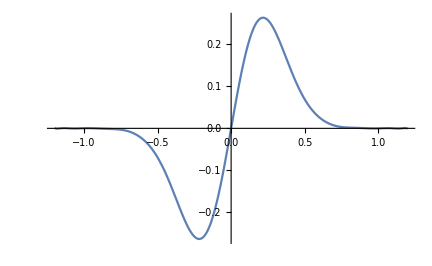

```mathematica
Plot[form[x],{x,-1.2,1.2}]
```

```mathematica
form[z]
```

1.98844 z-20.6594 z^3.+101.756 z^5.-303.867 z^7.+591.433 z^9.-763.814 z^11.+647.044 z^13.-344.585 z^15.+104.411 z^17.-13.7072 z^19.